## Elliptic Potential V(q)

```mathematica
ClearAll["Global`*"]
```

## Constants

```mathematica
jConst=13/2;
thetaConst=-80; (*Degrees*)
moi1=95;
moi2=100;
moi3=85;
A1Const=1/(2*moi1);
A2Const=1/(2*moi2);
A3Const=1/(2*moi3);
```

## Formulas

```mathematica
jvec[j_,theta_]:={j*Cos[theta*π/180],j*Sin[theta*π/180],0};
jk[k_,j_,theta_]:=N[jvec[j,theta][[k]]];
A12term[I_,j_,theta_,A1_,A2_]:=A2*(1-jk[2,j,theta]/I)-A1;
v0term[I_,j_,theta_,A1_,A2_]:=-(A1*jk[1,j,theta])/A12term[I,j,theta,A1,A2];
uterm[I_,j_,theta_,A1_,A2_,A3_]:=(A3-A1)/A12term[I,j,theta,A1,A2];
kterm[I_,j_,theta_,A1_,A2_,A3_]:=Sqrt[Abs[uterm[I,j,theta,A1,A2,A3]]];
```

```mathematica
phi[q_,k_]:=JacobiAmplitude[q,k^2];
s[q_,k_]:=Sin[phi[q,k]];
c[q_,k_]:=Cos[phi[q,k]];
d[q_,k_]:=Sqrt[1-k^2*s[q,k]^2];
```

```mathematica
VT1[q_,I_,j_,theta_,A1_,A2_,A3_]:=(I*(I+1)*kterm[I,j,theta,A1,A2,A3]^2+v0term[I,j,theta,A1,A2]^2)*s[q,kterm[I,j,theta,A1,A2,A3]]^2;
VT2[q_,I_,j_,theta_,A1_,A2_,A3_]:=(2I+1)*v0term[I,j,theta,A1,A2]*c[q,kterm[I,j,theta,A1,A2,A3]]*d[q,kterm[I,j,theta,A1,A2,A3]];
V[q_,I_,j_,theta_,A1_,A2_,A3_]:=VT1[q,I,j,theta,A1,A2,A3]+VT2[q,I,j,theta,A1,A2,A3];
```

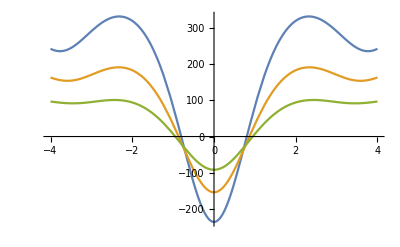

```mathematica
Plot[{V[q,45/2,jConst,thetaConst,A1Const,A2Const,A3Const],V[q,37/2,jConst,thetaConst,A1Const,A2Const,A3Const],V[q,29/2,jConst,thetaConst,A1Const,A2Const,A3Const]},{q,-4,4}]
```

```mathematica
(*Plot[{JacobiSN[q,kterm[I,jConst,thetaConst,A1Const,A2Const,A3Const]^2],s[q,kterm[I,jConst,thetaConst,A1Const,A2Const,A3Const]]},{q,0,7},PlotStyle->{{Red,Thick},{Black,Dashed}}]*)
```